```mathematica
Clear[g0,v0]
x[t_,θ_]:=Module[{},
t v0 Cos[θ]
]
y[t_,θ_]:=Module[{},
-g t^2/2 + v0 Sin[θ] t + 100
]
```

```mathematica
tsub=(20 Csc[θ])/g;
```

```mathematica
{x[tsub,θ],y[tsub,θ]}
```

{(20 v0 Cot[θ])/g,100+(20 v0)/g-(200 Csc[θ]^2)/g}

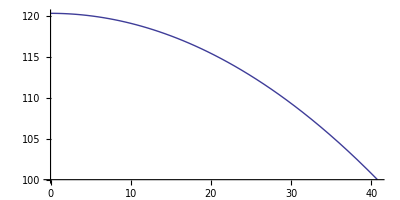

```mathematica
ParametricPlot[{x[tsub,θ],y[tsub,θ]}/.{g->9.81,v0->20},{θ,Pi/4,Pi/2}]
```

```mathematica
vl=Pi x[tsub,θ]^2 D[y[tsub,θ],θ]
```

(160000 π v0^2 Cot[θ]^3 Csc[θ]^2)/g^3

```mathematica
?SetPrecision
```

SetPrecision[expr,p] yields a version of expr in which all numbers have been set to have precision p.

```mathematica
SetPrecision[
outvl=Integrate[vl,{θ,Pi/4,Pi/2}];
a1=N[outvl/.{v0->20.000,g->9.81000},10],20]
```

53243.038643253552436

```mathematica
SetPrecision[
outvl=NIntegrate[vl,{θ,Pi/4-0.4,Pi/2}];
a1=N[outvl/.{v0->20.000,g->9.81000},10],20]
```

1.9656413553146065678×10^6

```mathematica
vls=Solve[y[t,Pi/4]==0,t]
x[t,Pi/4]
```

{{t→-(-√2 v0+√2 √(400 g+v0^2))/(2 g)},{t→(√2 v0+√2 √(400 g+v0^2))/(2 g)}}

(t v0)/(√2)

```mathematica
(√2 v0+√2 √(400 g+v0^2))/(2 g)/.{v0->20,g->9.81}
```

6.18139

```mathematica
y[0,θ]
```

100

```mathematica
dxdt2=D[x[t,Pi/4],t];
dydt2=D[y[t,Pi/4],t];
t1=(20 Csc[Pi/4])/g;
SetPrecision[
intvl=Integrate[Pi x[t,Pi/4]^2dydt2,{t,t1,tint[Pi/4]}];
Abs[intvl]+a1,20]
```

1.5679234411338712089×10^6

```mathematica
Integrate[2 Pi x[t,Pi/4] Sqrt[dxdt2^2+dydt2^2],{t,0,4tint[Pi/4]}]
```

4.03534×10^6

```mathematica
tint[Pi/4]
```

6.18139

```mathematica
dydt2
```

10 √2-9.81 t

```mathematica
y[t,Pi/4]
```

100+10 √2 t-4.905 t^2